```mathematica
Clear["Global`*"];
SeedRandom[0];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"Sampler1`";
```

```mathematica
U[x_,y_]=10000/2(√(x^2+y^2)-10)^2;
dU[x_,y_]=GradientG[U[x,y],{x,y}];
ddU[x_,y_]=HessianH[U[x,y],{x,y}];
```

501 218.456 11.1489 0.890862 0.15159 4.13639 222.592 224.842 0.00016424 0.0251638 True {1,2,9,11} {1,11}

1002 188.762 0.0553693 0.337864 0.373486 3.26343 173.11 192.026 0.000387269 0.033493 False {1,2,5,11} {1,2,8,11}

1503 146.26 11.5352 0.446859 0.368051 1.69621 147.956 110.166 0.000468595 0.0445792 True {1,2,11} {1,11}

2004 150.169 0.387589 0.870001 0.123577 5.26331 84.1608 155.432 0.000387269 0.0445792 False {1,11} {1,6,7,10,11}

2505 77.668 17.1752 0.715616 0.322362 6.4928 84.1608 159.051 0.000425996 0.0445792 True {1,2,7,9,11} {1,11}

3006 138.859 0.414937 0.750129 0.273506 3.32432 100.239 142.184 0.000468595 0.0445792 False {1,4,11} {1,5,6,11}

3507 97.2516 11.7489 0.414699 0.375788 2.98761 100.239 145.635 0.000567 0.0368423 True {1,2,11} {1,11}

4008 147.156 -0.0926448 0.468568 0.356587 3.32921 109.713 150.485 0.0006237 0.0445792 False {1,3,11} {1,2,4,11}

4509 106.679 6.19806 0.517345 0.387527 3.03432 109.713 198. 0.000567 0.0368423 True {1,2,3,4,11} {1,11}

5010 195.148 0.111547 0.71568 0.356755 6.8387 119.652 201.987 0.000515455 0.033493 False {1,3,11} {1,5,9,11}

5511 114.653 10.8851 0.362605 0.42656 4.99954 119.652 201.987 0.000515455 0.033493 True {1,2,11} {1,11}

6012 195.852 1.77596 0.770761 0.414814 6.13518 119.652 201.987 0.000515455 0.033493 False {1,3,11} {1,3,4,5,11}

6513 116.569 10.5943 0.559326 0.444189 3.08353 119.652 201.987 0.000515455 0.033493 True {1,6,8,11} {1,6,11}

7014 199.976 -8.48457 0.700759 0.439599 2.01081 119.652 201.987 0.000515455 0.033493 False {1,11} {1,2,11}

7515 113.055 5.54571 0.500064 0.413472 6.59764 119.652 201.987 0.000515455 0.033493 True {1,4,7,11} {1,2,11}

8016 199.777 0.153817 0.396364 0.347058 2.2099 119.652 201.987 0.000515455 0.033493 False {1,2} {2,3,8,11}

8517 111.717 6.96611 0.79897 0.379277 7.93524 119.652 201.987 0.000515455 0.033493 True {1,6,11} {1,4,9,11}

9018 194.904 6.57075 0.797302 0.410863 7.08315 119.652 201.987 0.000515455 0.033493 False {1,11} {1,2,7,11}

9519 116.412 8.70155 0.664967 0.40629 3.23988 119.652 201.987 0.000515455 0.033493 True {1,2,6,8,11} {1,11}

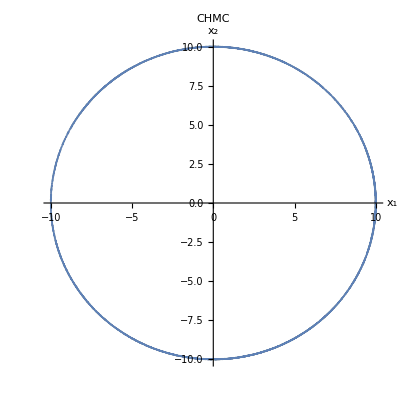

```mathematica
QS=hmc[U,dU,ddU,2,5000,10000,True,True];
ListPlot[QS,AspectRatio->1,PlotStyle->Opacity[0.1],AxesLabel->{"x_1","x_2"},PlotStyle->{Green},PlotLabel->CHMC]
```

501 71.3301 6.50747 0.690936 0.385314 6.29859 77.6286 3.68226×10^6 0.000290961 0.0001 True {1,11} {1,11}

1002 98.2986 6.41707 0.638392 0.391513 3.70057 101.999 3.68226×10^6 0.000468595 0.0001 True {1,2,6,11} {1,3,11}

1503 104.164 9.76883 0.758319 0.361444 5.70458 109.868 3.68226×10^6 0.000425996 0.0001 True {1,8,9,10,11} {1,9,11}

2004 80.1616 11.9427 0.861135 0.219765 2.38257 82.5442 3.68226×10^6 0.000515455 0.0001 True {1,2,7,10,11} {1,11}

2505 83.9748 7.39178 0.843303 0.242135 2.20879 86.1836 3.68226×10^6 0.000425996 0.0001 True {1,4,6,11} {1,4,9,11}

3006 91.5892 10.6742 0.611489 0.354823 2.48779 94.077 3.68226×10^6 0.000468595 0.0001 True {1,2,6,10,11} {1,11}

3507 60.5451 14.4621 0.470395 0.328264 3.24196 63.7871 3.68226×10^6 0.000567 0.0001 True {1,2,11} {1,4,11}

4008 40.4552 9.07167 0.644756 0.334668 2.07113 42.5264 3.68226×10^6 0.000567 0.0001 True {1,2,3,6,7,8} {1,11}

4509 63.5512 12.9229 0.580948 0.424916 2.41879 65.97 3.68226×10^6 0.0006237 0.0001 True {1,2,3,8,11} {1,11}

5010 62.9841 12.3518 0.658857 0.410649 2.98593 65.97 3.68226×10^6 0.000567 0.0001 True {1,2,5,10,11} {1,11}

5511 60.5626 10.5899 0.644776 0.37364 5.40739 65.97 3.68226×10^6 0.000567 0.0001 True {1,2,4,5,11} {1,11}

6012 56.2781 10.9391 0.751201 0.407527 9.69188 65.97 3.68226×10^6 0.000567 0.0001 True {1,8,11} {1,11}

6513 60.8309 10.2852 0.546966 0.44973 5.13913 65.97 3.68226×10^6 0.000567 0.0001 True {1,2,5,8,11} {1,9,11}

7014 63.0654 13.3026 0.480278 0.311569 2.90459 65.97 3.68226×10^6 0.000567 0.0001 True {1,2,3} {10,11}

7515 60.3251 9.02466 0.576448 0.356713 5.64484 65.97 3.68226×10^6 0.000567 0.0001 True {1,2,7,11} {1,11}

8016 63.3998 8.43912 0.510121 0.365718 2.57018 65.97 3.68226×10^6 0.000567 0.0001 True {1,4,6,11} {1,11}

8517 64.1896 7.78933 0.59412 0.342432 1.78035 65.97 3.68226×10^6 0.000567 0.0001 True {1,2,5,11} {6,11}

9018 62.2714 10.4565 0.693611 0.412581 3.69859 65.97 3.68226×10^6 0.000567 0.0001 True {1,7,8,11} {1,10,11}

9519 60.4108 13.7397 0.82366 0.306282 5.55922 65.97 3.68226×10^6 0.000567 0.0001 True {1,2,3,4,6,7,11} {1,10,11}

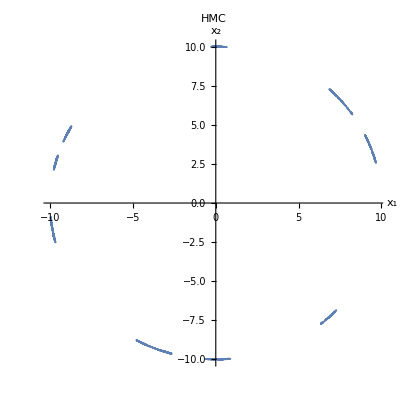

```mathematica
QS=hmc[U,dU,ddU,2,5000,10000,True,False];
ListPlot[QS,AspectRatio->1,PlotStyle->Opacity[0.1],AxesLabel->{"x_1","x_2"},PlotStyle->{Green},PlotLabel->HMC]
```

501 474.209 64.4154 0.498285 0.404825 13.4406 421.703 487.65 1.×10^-9 0.0368423 False {1,2,6,11} {1,11}

1002 340.462 71.4287 0.6403 0.356855 12.0036 421.703 352.466 1.×10^-9 0.0304482 False {1,4,9,11} {1,11}

1503 343.65 100.412 0.689192 0.329926 8.81553 421.703 352.466 1.×10^-9 0.0405265 False {1,11} {1,11}

2004 288.649 51.5523 0.512591 0.436379 4.10177 421.703 292.751 1.×10^-9 0.0490371 False {1,2,8,9,10,11} {1,3,10,11}

2505 67.8439 35.0231 0.691159 0.315898 6.7023 421.703 74.5462 1.×10^-9 0.0593349 False {1,6,7,11} {1,11}

3006 74.6301 33.0698 0.676525 0.406434 6.46625 421.703 81.0963 1.×10^-9 0.0789747 False {1,2,3,7,8,9,11} {1,3,7,11}

3507 68.0497 64.0903 0.621129 0.35225 7.12667 421.703 75.1764 1.×10^-9 0.0955594 False {1,4,6,10,11} {1,7,8,10,11}

4008 73.8704 38.1322 0.610274 0.370495 8.41852 421.703 82.289 1.×10^-9 0.0955594 False {1,2,8,11} {1,3,8,9,11}

4509 88.7035 744.773 0.772607 0.351503 1.47487 421.703 90.1783 1.×10^-9 0.0868722 False {1,8,11} {1,2,4,7,8,11}

5010 48.7168 119.82 0.790589 0.182018 3.70741 421.703 52.4242 1.×10^-9 0.0717952 False {1,4,11} {1,11}

5511 47.1755 63.4588 0.763996 0.215631 5.24866 421.703 52.4242 1.×10^-9 0.0717952 False {1,5,11} {1,5,8,11}

6012 46.8695 43.8642 0.815554 0.225076 5.55473 421.703 52.4242 1.×10^-9 0.0717952 False {1,11} {1,6,9,11}

6513 48.5954 158.234 0.8557 0.224137 3.8288 421.703 52.4242 1.×10^-9 0.0717952 False {1,7,11} {1,4,5,11}

7014 47.1025 36.9443 0.65318 0.369763 5.32168 421.703 52.4242 1.×10^-9 0.0717952 False {1,9,11} {1,10,11}

7515 47.3418 86.1131 0.627877 0.275163 5.08243 421.703 52.4242 1.×10^-9 0.0717952 False {1,11} {5,10,11}

8016 47.9722 64.7519 0.711284 0.235144 4.45202 421.703 52.4242 1.×10^-9 0.0717952 False {1,2,4} {7,11}

8517 46.534 21.7516 0.721427 0.304659 5.89023 421.703 52.4242 1.×10^-9 0.0717952 False {1,2,3,4,6,11} {1,5,11}

9018 47.5559 72.0033 0.728188 0.249429 4.86831 421.703 52.4242 1.×10^-9 0.0717952 False {1,2,11} {1,4,11}

9519 48.9477 27.7752 0.63883 0.375847 3.4765 421.703 52.4242 1.×10^-9 0.0717952 False {1,5,7,8,11} {1,11}

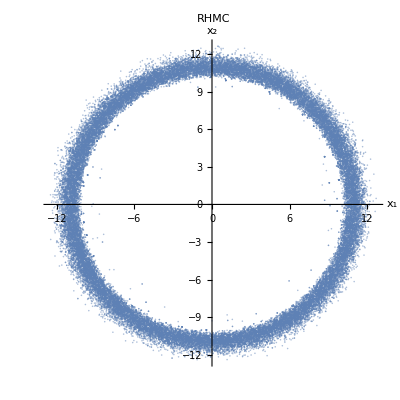

```mathematica
U[x_,y_]=1/2(√(x^2+y^2)-10)^2;
dU[x_,y_]=GradientG[U[x,y],{x,y}];
ddU[x_,y_]=HessianH[U[x,y],{x,y}];
QS=hmc[U,dU,ddU,2,5000,10000,False,False];
ListPlot[QS,AspectRatio->1,PlotStyle->Opacity[0.5],AxesLabel->{"x_1","x_2"},PlotStyle->{Green},PlotLabel->RHMC]
```